## Introduction

### Parameter estimates

Adult worms survive for up to six weeks in their hosts, so we estimate the rate of host recovery ρ=0.024 days-1 (Komiya et al. 1956). 
Eggs develop into larvae at a rate of 0.044/day (Foster and Daengsvang 1932). 
Scat loses infecting ability as the number of live larvae in it die. We use the mean survival duration of larvae, and obtain μ_L=0.152/day. Similarly, egg mortality is estimated μ_E=0.069/day. 
The probability of infection given contact is very high for dogs and A. caninum, around 0.97. In contrast, the probability is <1/12 (combined oral and dermal exposure) for cats exposed to this dog parasite. We scale these values by 50% and obtain κ_D=0.97 2=0.485 and κ_W=0.042. The estimated proportion σ of compatibility is thus κ_W/κ_D=0.083/0.97=0.086.
The cat defecation rate was taken from a study of leopards, and is estimated at λ_W=1.667/day.
In a study of rural dogs in cacao plantations, 10 dogs were observed for six days each, and 87 defecation events were observed (dos Santos et al. 2018. J. Mamm. 99:1261). The estimate defecation rate is then λ_D=82/(10 6)=1.37. 
FInally, the coefficient of overlap was estimated as ω=0.358 based on camera-trap surveys. This estimate was based on frequencies of use of trails of 0.024/day for ocelots, and 0.067/day for dogs. These were likely overestimates. I have corrected the calculation, and obtained frequencies of 0.087/day for dogs, and 0.22 for ocelots. I use the value for ocelots as the x value in the contour plots. This assumes that about 1/5 of ocelot interactions with scat, be it depositing or picking up, will occur on “domestic” habitats. This is likely higher than the true value.

## Model with single pool

### Estimation of β

I estimate β based on the observed prevalence in domestic dogs, and the value it would take to reach that prevalence at equilibrium. First I create a function that estimates the prevalence at equilibrium. Then I plot the difference between the observed and the estimated prevalence for the domestic species. We see that β is around 0.0024 when including the wild species, 0.0021 when including only the dogs.

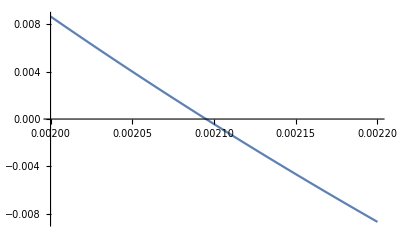

```mathematica
betaest[β_]:=With[{κd=0.485,κw=1/12/2,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=0 0.358},
Id[700]/(Sd[700]+Id[700])/.NDSolve[
{Sd'[t]==-κd β Sd[t] L[t]+ρ Id[t],
Id'[t]==κd β Sd[t] L[t]-ρ Id[t],
L'[t]==δ λ (ω Iw[t]+Id[t])/(δ+μe)-μl L[t]-β L[t](Sd[t]+Id[t]+ω(Sw[t]+Iw[t])),
Sw'[t]==-ω κw β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω κw β Sw[t]L[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, L[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,L,Sd,Sw},
{t,0,700}]];
Plot[0.742-betaest[β],{β,0.0020,0.0022}]
```

### Scenario 1: Spillover from dogs to cats

Under the first scenario, the parasite is maintained by dogs, but it can be acquired from the environment by wild felines. This scenario then assumes λ_W=0.

```mathematica
With[{κd=0.97/2,κw = 1/12/2,
λw=0,λd=82/60,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=1. 0.358,
β=0.0021},
nsol1=NDSolve[
{Sd'[t]==-κd β Sd[t] L[t]+ρ Id[t],
Id'[t]==κd β Sd[t] L[t]-ρ Id[t],
L'[t]==δ (ω λw Iw[t]+λd Id[t])/(δ+μe)-μl L[t]-β L[t](Sd[t]+Id[t]+ω(Sw[t]+Iw[t])),
Sw'[t]==-ω  κw β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω  κw β Sw[t]L[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, L[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,L,Sd,Sw},
{t,0,700}]];
```

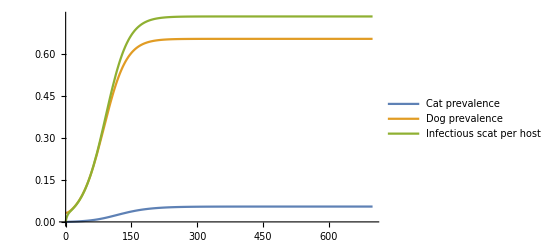

```mathematica
Plot[Evaluate[{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t]),L[t]/(Sd[t]+Id[t]+Sw[t]+Iw[t])}/.nsol1],{t,0,700},
PlotLegends->{"Cat prevalence","Dog prevalence","Infectious scat per host"}, LabelStyle->"Subsubtitle"]
```

```mathematica
With[{t=700},{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t])}/.nsol1]
```

{{0.0546791,0.652858}}

The expected prevalence in wild cats would be 5.5%, 65.3% in domestic dogs.

### Scenario 2: Multi-host parasite

#### Single pool

In this scenario, cats do contribute to the pool (λ_□>0)

```mathematica
With[{κd=0.97/2,κw = 1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=1. 0.358,
β=0.0021},
nsol2=NDSolve[
{Sd'[t]==-κd β Sd[t] L[t]+ρ Id[t],
Id'[t]==κd β Sd[t] L[t]-ρ Id[t],
L'[t]==δ (ω λw Iw[t]+λd Id[t])/(δ+μe)-μl L[t]-β L[t](Sd[t]+Id[t]+ω(Sw[t]+Iw[t])),
Sw'[t]==-ω  κw β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω  κw β Sw[t]L[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, L[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,L,Sd,Sw},
{t,0,700}]];
```

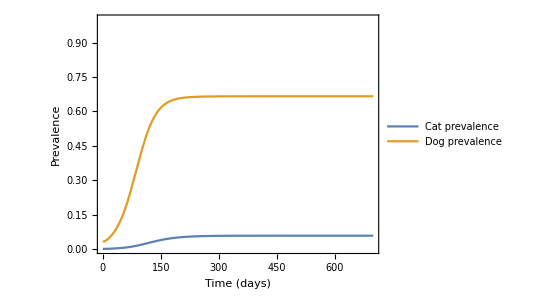

```mathematica
Plot[Evaluate[{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t])}/.nsol2],{t,0,700},
PlotLegends->{"Cat prevalence","Dog prevalence"},
LabelStyle->"Subsubtitle",
Frame->True,
FrameLabel->{"Time (days)","Prevalence"},
(*LabelStyle->Large,ImageSize->Large,*)
PlotRange->{Automatic,{0,1}},
PlotStyle->Thick, AspectRatio->3/4]
```

```mathematica
With[{t=700},{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t])}/.nsol2]
```

{{0.0576647,0.665512}}

The expected prevalences are nearly identical when you include the contribution from cats, suggesting cats have only a small influence on the overall dynamics of the parasite.

#### Contour Plot for different scenarios

For the Fields workshop, I will explore different scenarios. I can use the expected prevalence analytical solution, which depends on the initial conditions

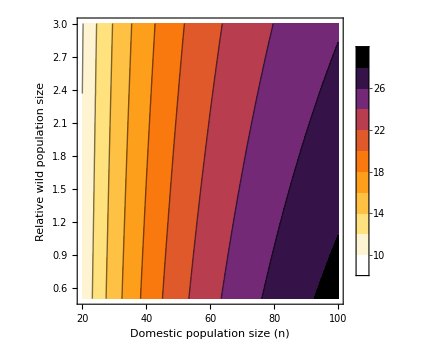
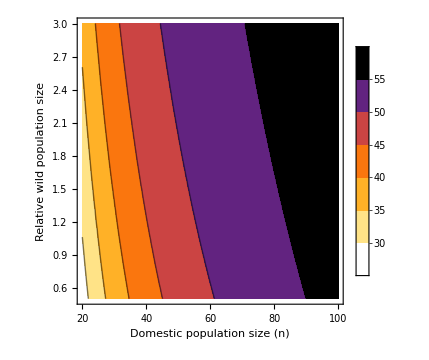
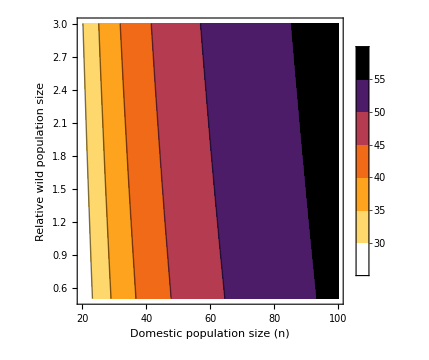
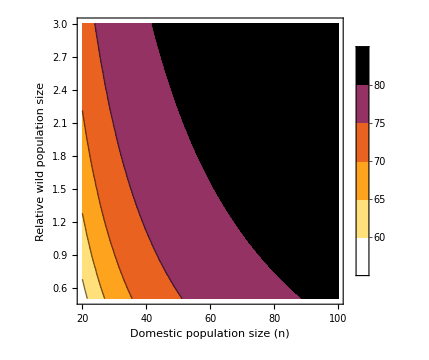

```mathematica
Table[ContourPlot[Evaluate[100*Iw[10000]/(Iw[10000]+Sw[10000])/.nsolf[{a-1,1,0,a*x,0}, c,o]],{a,20,100},{x,0.5,3},
FrameLabel->{"Domestic population size (n)","Relative wild population size"},
LabelStyle->Large,ImageSize->Medium,
ColorFunction->ColorData[{"SunsetColors","Reverse"}],
PlotLegends->Automatic],{c,{0.25,0.75}},{o,{0.25,0.75}}]
```

### Scenario 1: Parallel, shared pools

In the first scenario, dogs do not have access to the pool associated with cats. This pool would represent the scat deposited by wild cats in the forest, where dogs go infrequently. This is represented by the ω parameters. Setting ω_D=1 means that all the scat from dogs is deposited in the first pool. Meanwhile, wild animals deposit 35.8% of their scat in the first pool and the rest in the second. In this scenario the compatibility of the parasite with the wild host is low.

#### Expected prevalence

```mathematica
With[{κd=0.97/2,κw = 1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ωw=0.358,ωd=1,
βd1=0.0021, βd2=0.0021, βw1=0.0021, βw2=0.0021},
First[{Iw[700]/(Iw[700]+Sw[700]),Id[700]/(Id[700]+Sd[700])}/.
NDSolve[
{Sd'[t]==-κd βd1 Sd[t] L1[t]+ρ Id[t],
Id'[t]==κd βd1 Sd[t] L1[t]-ρ Id[t],
E1'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe E1[t]-δ E1[t],
E2'[t]==λw Iw[t]-ωw λw Iw[t]+ (1-ωd)λd Id[t]-μe E2[t]-δ E2[t],
L1'[t]==δ E1[t]-μl L1[t]-βd1 ωd L1[t](Sd[t]+Id[t])-βw1 ωw L1[t](Sw[t]+Iw[t]),
L2'[t]==δ E2[t]-μl L2[t]- (1-ωd)βd2 L2[t](Sd[t]+Id[t])-βw2 (1-ωw) L2[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw  κw βw1 Sw[t]L1[t]-(1-ωw)  κw βw2 Sw[t]L2[t]+ρ Iw[t],
Iw'[t]==ωw  κw βw1 Sw[t]L1[t]+(1-ωw)  κw βw2 Sw[t]L2[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, L1[0]==0,L2[0]==0,E1[0]==0,E2[0]==0,Sw[0]==29,Iw[0]==0},
{Id,Iw,L1,L2,E1,E2,Sd,Sw},
{t,0,700}]
]]
```

{0.067097,0.66803}

We obtain an expected prevalence of 6.7% in wild hosts, and 66.8% in domestic hosts.

### Scenario 3: Separate cycles

I create a function that gives the numerical solution as a function of the initial values, compatibility and overlap. Using the function we can plot the prevalence at equilibrium for different population sizes. The prevalence at equilibrium depends on the population sizes. I explore a wide range of population sizes, from 20 to 100 dogs, and 10 to 200 wild animals. The prevalence changes between 2% and 6%. The greatest variation is caused by the number of dogs.

```mathematica
nsolf[init_,compatibility_,overlap_]:=
With[
{κd=0.485,σ=compatibility,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=1. 0.358,
β=0.0021},
nsol=NDSolve[
{Sd'[t]==-κd β Sd[t] L[t]+ρ Id[t],
Id'[t]==κd β Sd[t] L[t]-ρ Id[t],
L'[t]==δ (ω λw Iw[t]+λd Id[t])/(δ+μe)-μl L[t]-β L[t](Sd[t]+Id[t]+ω(Sw[t]+Iw[t])),
Sw'[t]==-ω  σ κd β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω σ κd β Sw[t]L[t]-ρ Iw[t],
Sd[0]==init[[1]], Id[0]==init[[2]], L[0]==init[[3]],Sw[0]==init[[4]],Iw[0]==init[[5]]},
{Id,Iw,L,Sd,Sw},
{t,0,10000}]];
```

#### Recovery rate sensitivity analysis

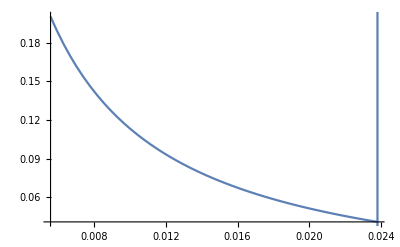

```mathematica
Show[{
Plot[
With[{κ=0.485,σ=0.046,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ω=0.358,
β=0.0021,
init={29,1,0,30,0}},
First[Iw[10000]/(Iw[10000]+Sw[10000])/.NDSolve[
{Sd'[t]==-κ β Sd[t] L[t]+ρ Id[t],
Id'[t]==κ β Sd[t] L[t]-ρ Id[t],
L'[t]==δ λ (ω Iw[t]+Id[t])/(δ+μe)-μl L[t]-β L[t](Sd[t]+Id[t]+ω(Sw[t]+Iw[t])),
Sw'[t]==-ω σ κ β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω σ κ β Sw[t]L[t]-ρ Iw[t],
Sd[0]==init[[1]], Id[0]==init[[2]], L[0]==init[[3]],Sw[0]==init[[4]],Iw[0]==init[[5]]},
{Id,Iw,L,Sd,Sw},
{t,0,10000}]]
],
{ρ,1/180,1/42}
],
ListLinePlot[{{1/42,0},{1/42,1}}]
}
]
```

Slower recovery rates would bring the expected prevalence up. For six months you would get 20% prevalence.

#### Contour plot

The values change mostly as a function of ω, the level of overlap, and σ, the relative compatibility. We can determine how changes in each of these parameters would influence the prevalence in ocelots. The prevalence in dogs will change as well but less significantly.

```mathematica
Show[
ContourPlot[First[Iw[10000]/(Iw[10000]+Sw[10000])/.nsolf[{29,1,0,30,0}, σ,ω]],{ω,0.001,1},{σ,0.001,0.5},
Contours->{1,2,5,10,20,40,60,80}/100,
FrameLabel->{"Habitat overlap (ω)","Host compatibility (σ)"}, 
(*ContourLabels->(Style[Text[#3,{#1,#2}], Large,White]&),*)
LabelStyle->Large,ImageSize->Large,
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[First[Iw[10000]/(Iw[10000]+Sw[10000])/.nsolf[{29,1,0,30,0}, σ,ω]],{ω,0.001,1},{σ,0.001,0.5},
Contours->{6.9,52.8}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[First[Iw[10000]/(Iw[10000]+Sw[10000])/.nsolf[{29,1,0,30,0}, σ,ω]],{ω,0.001,1},{σ,0.001,0.5},
Contours->{25}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{PointSize[Large],White,Point[{0.358,0.086}],
Text[Style["1%",FontSize->16],{0.12,0.045}],
Text[Style["2%",FontSize->16],{0.16,0.07}],
Text[Style["5%",FontSize->16],{0.22,0.11}],
Text[Style["10%",FontSize->16],{0.3,0.16}],
Text[Style["20%",FontSize->16],{0.41,0.23}],
Text[Style["40%",FontSize->16],{0.64,0.33}],
Text[Style["60%",FontSize->16],{0.9,0.42}]}]
]
```

-Graphics-

Given these values, in particular the host compatibility, the expected prevalence in ocelots under the scenario of dog-to-cat spillover is falls just inside the estimated prevalence

29-1-24
I don’t know where the 0.03 compatibility came from. The values I have for infectivity (probability of infection given contact) are 0.97 for dogs, and 1/6 for cats. I divide both by half assuming much lower infectivity in natural than experimental settings. We then get κ=0.458 for dogs, and κ=0.083 for cats. The proportion would be 0.458/0.083, or 0.17, which fits perfectly within the predicted prevalence range for ocelots.

## Model with parallel pools

February 2024
Another potential representation is that there are two separate pools of infectious stages, one mostly associated with the wild hosts and one more associated with the domestic hosts. This model lets us explore the parameter space of proportion of scat shed in each pool. The model is represented by the following system of ODEs:

dS_D/dt=ρ_D I_D-ω_D β_H κ_D L_H S_D-(1-ω_D)β_N κ_D L_N S_D
dI_D/dt=-ρ_D I_D+ω_D β_H κ_D L_H S_D+(1-ω_D)β_N κ_D L_N S_D
dE_1/dt=ω_W λ_W I_W+ω_D λ_D I_D-μ_E E_H-δ E_H-
dE_2/dt=(1-ω_W)λ_W I_W+(1-ω_D)λ_D I_D-μ_E E_2-δ E_2
dL_1/dt=δ E_1-μ_L L_1-β_D1 L_1(S_D+I_D)-β_W1 L_1(S_W+I_W)
dL_1/dt=δ E_2-μ_L L_2-β_D2 L_2(S_D+I_D)-β_W2 L_2(S_W+I_W)
dS_W/dt=ρ_W I_W-ω_W β_W κ_W L_1 S_W-(1-ω_W)β_W κ_W L_2 S_W
dI_W/dt=-ρ_W I_W+ω_W β_W κ_W L_1 S_W+(1-ω_W)β_W κ_W L_2 S_W

The shedding rates λ and the infection rates β are scaled by coefficient of overlap ω that represent the proportion of interactions in each habitat. Thus, the proportion of scat that dogs deposited and interact with in their own pool is high, while the proportion for wild hosts in the “domestic” pool is low.

#### Exploration of β

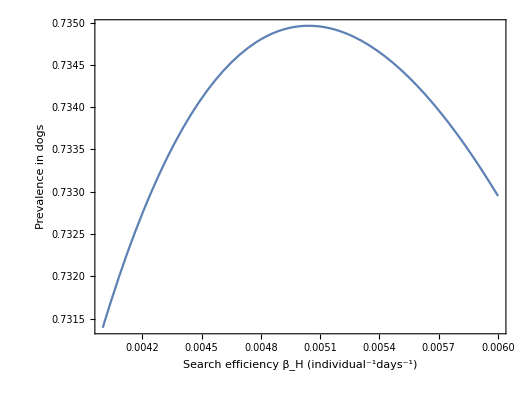

```mathematica
ndsolb[βn_,βh_]:= With[{κd=0.97/2,κw=1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
ωd=1,ωw=0},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
With[{finalt = 700},
Plot[Id[finalt]/(Id[finalt]+Sd[finalt])/.ndsolb[1,βh],{βh,0.004,0.006}, Frame->True, FrameLabel->{"Search efficiency β_H (individual^-1days^-1)", "Prevalence in dogs"}, LabelStyle->18, AspectRatio->3/4]]
```

With the two-pool model, the β parameter estimate that would produce the maximum prevalence in dogs (57%) is β=0.0044. We assume search efficiency is lower in the forest, since scat will be more spread out. A conservative estimate is that β_W=β_D/2=0.0044/2=0.0022.

```mathematica
Id[700]/(Id[700]+Sd[700])/.ndsolb[1,0.0043]
```

{0.570388}

#### One-directional transmission scenario

One potential scenario is that cats acquire a parasite of dogs, yet they do not transmit it. This is equivalent to setting λ_W=0.

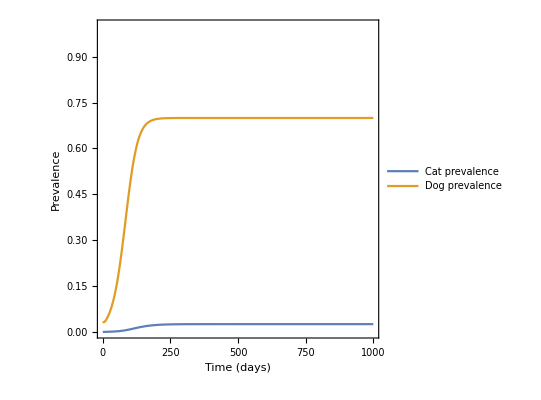

```mathematica
With[{κd=0.97/2,κw = 1/12/2,
λw=0,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
ωw=0.13,ωd=1,
βh=0.005, βn=0.005/2},
Plot[Evaluate[{Iw[t]/(Iw[t]+Sw[t]),Id[t]/(Id[t]+Sd[t])}/.
NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,1000}]],
{t,0,1000},PlotLegends->{"Cat prevalence","Dog prevalence"},
LabelStyle->"Subsubtitle",
Frame->True,
FrameLabel->{"Time (days)","Prevalence"},
(*LabelStyle->Large,ImageSize->Large,*)
PlotRange->{Automatic,{0,1}},
PlotStyle->Thick, AspectRatio->1]]
```

#### Different degrees of overlap

The contour plot explores how the expected prevalence in wild hosts at equilibrium changes with respect to changes in parameter values. We explore how higher overlap would change the expected prevalence, by modifying the ω parameters. The ω_i parameter represents the proportion of scat that  host species i interacts with in the “domestic” pool (Pool 1), and (1-ω) represents the proportion in the “wild” pool.

```mathematica
ndsol = With[{κd=0.97/2,κw = 1/12/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
(*ωw=0.358,ωd=1,*)
βh=0.005, βn=0.005/2},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   κw βh Sw[t]Lh[t]-(1-ωw)   κw βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   κw βh Sw[t]Lh[t]+(1-ωw)   κw βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol,{ωw,0.01,0.5},{ωd,0.7,1},
(*Contours->N[Table[x/10,{x,1,9}]],*)
FrameLabel->{"Contribution wild hosts (ω_W)","Contribution domestic hosts (ω_D)"}, 
ContourLabels->(Style[Text[#3,{#1,#2}], 12, White]&),
LabelStyle->16,ImageSize->400,
ColorFunction->"AvocadoColors",
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[First[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol],{ωw,0.01,0.5},{ωd,0.7,1},
Contours->{6.9,52.8}/100,
ContourShading->{None,{Opacity[0.8,Black],HatchFilling[]},None},
ContourStyle->Opacity[0.8,Black]],
ContourPlot[First[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsol],{ωw,0.01,0.5},{ωd,0.7,1},
Contours->{25}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]]]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

-Graphics-

Under realistic levels of overlap, would expect between <3%  prevalence of dog hookworms in wild hosts.

#### Different overlap and compatibility

We can explore how changes in compatibility change these conclusions. In scenario 1 (a parasite of dogs), we have κd=0.97/2,   βw=0.0035/2, and two values of ω_D:1 and 0.7. In scenario 2 (a parasite species/population specific to cats), we have κd=0.5/2, ωd=1, and two values of β_W:0.0044/2 and 0.0044/5.

```mathematica
ndsolk[ωw_,ωd_,σ_]:= With[{κd=0.97/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.069,
ρ=1/42,
βh=0.005,βn=0.005/2},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   σ κd βh Sw[t]Lh[t]-(1-ωw)  σ κd βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   σ κd βh Sw[t]Lh[t]+(1-ωw)   σ κd βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
```

```mathematica
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{0.01,0.02,0.05,0.1,0.2,0.3,0.4,0.5},
(*ContourLabels->None,*)
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,1,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,0.086}]
}]]]
```

-Graphics-

```mathematica
Export["C:\\Users\\juans\\OneDrive - University of Toronto\\Feline Parasite Chapter\\Fig4_PeqContPlot_mod-b.pdf",
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,0.7,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{0.01,0.02,0.05,0.1,0.2,0.3,0.4,0.5},
ContourLabels->None,
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,0.7,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk[ωw,0.7,σ],{ωw,0.0,0.5},{σ,0,0.5},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,0.086}]
}]]], 
ImageResolution->300,ImageSize->300];
```

Host compatibility could drastically change the expected prevalence, and we would expect to see much higher prevalence in wild ocelots. For example if the probability of infection was just as high as it is for dogs then we would expect values greater than 60%, with the contribution of both hosts. Even if it was just half as infective in cats as it is in dogs, we would expect greater than 50% prevalence, even with no interaction of domestic hosts with scats in the “wild” pool. This is not what we observe, however. Given the estimated values of compatibility and overlap, we would expect nearly 10% prevalence in wild animals, much lower than the estimated prevalence (although within the confidence interval). To obtain values closer to the estimated prevalence compatibility would have to be greater, around 20% of the infectivity of the parasite in its native host. Increased overlap would only have a minor effect if domestic dogs contribute to the wild pool.

#### Parallel pools

There is another scenario where there are two parasite populations, or two separate species each specific to their host. In this case the probability of infection is similarly high for both hosts with their respective parasite, but the cycles are separate. For the parameters, we assume that environmental stages are similar, so mortality and development in the environment remain the same. Similarly, defecation rates are the same. We also assume similar survival in the host. Overlap parameters pertain to the host so they remain the same. The infectivity, however, does change. In this scenario, the compatibility of the parasite is higher in cats than in dogs, and dogs don’t contribute much (ω_D=1). Okoshi and Murata (1967) got positive infections in 6/6 of orally infected kittens, and 4/6 of dermally infected kittens. Put together we estimate κ_W=11/12=0.92. The opposite, A. tubaeforme infected 3/6 dogs exposed.

```mathematica
ndsolk2[ωw_,βn_,σ_]:= With[{κd=0.5/2,
λw=1/0.6,λd=82/60,
μl=1/6.6,δ=0.082,μe=0.071,
ρ=1/42,
ωd=0.7,
βh=0.005},NDSolve[
{Sd'[t]==-ωd κd βh Sd[t] Lh[t]-(1-ωd)κd βn Sd[t] Ln[t]+ρ Id[t],
Id'[t]==ωd κd βh Sd[t] Lh[t]+(1-ωd)κd βn Sd[t] Ln[t]-ρ Id[t],
Eh'[t]==λw  ωw Iw[t]+λd ωd Id[t]-μe Eh[t]-δ Eh[t]-βh  Eh[t](ωd(Sd[t]+Id[t])+ ωw(Sw[t]+Iw[t])),
En'[t]==(1-ωw) λw Iw[t]+ (1-ωd)λd Id[t]-μe En[t]-δ En[t]-βn  En[t]((1-ωd)(Sd[t]+Id[t])+(1- ωw)(Sw[t]+Iw[t])),
Lh'[t]==δ Eh[t]-μl Lh[t]-ωd βh  Lh[t](Sd[t]+Id[t])-ωw βh  Lh[t](Sw[t]+Iw[t]),
Ln'[t]==δ En[t]-μl Ln[t]- (1-ωd)βn Ln[t](Sd[t]+Id[t])-(1-ωw)βn  Ln[t](Sw[t]+Iw[t]),
Sw'[t]==-ωw   σ κd βh Sw[t]Lh[t]-(1-ωw)  σ κd βn Sw[t]Ln[t]+ρ Iw[t],
Iw'[t]==ωw   σ κd βh Sw[t]Lh[t]+(1-ωw)   σ κd βn Sw[t]Ln[t]-ρ Iw[t],
Sd[0]==29, Id[0]==1, Lh[0]==0,Ln[0]==0,Eh[0]==0,En[0]==0,Sw[0]==30,Iw[0]==0},
{Id,Iw,Lh,Ln,Eh,En,Sd,Sw},
{t,0,700}]];
```

```mathematica
With[{finalt = 700},
Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->N[Table[x/10,{x,1,9}]],
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.,.5},{σ,1,3},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/2,σ],{ωw,0.0,.5},{σ,1,3},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,1.84}]}]
]]
```

-Graphics-

```mathematica
0.97/2
```

0.485

```mathematica
48
```

```mathematica
With[{finalt = 700},
Export["C:\\Users\\juans\\OneDrive - University of Toronto\\Feline Parasite Chapter\\Fig4_PeqContPlot_mod-d.pdf",Show[
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->N[Table[x/10,{x,1,9}]],
LabelStyle->Directive[16,Black],
ColorFunction->"AvocadoColors",
ColorFunctionScaling->False,
ContourStyle->Directive[{White,Dashed}]],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->{7.6,56.5}/100,
ContourShading->{None,{White,HatchFilling[]},None},
ContourStyle->White],
ContourPlot[Iw[finalt]/(Iw[finalt]+Sw[finalt])/.ndsolk2[ωw,0.005/20,σ],{ωw,0.0,0.5},{σ,1,3},
Contours->{27.3}/100,
ContourShading->{None,None},
ContourStyle->Directive[White, Opacity[0.9], Thickness[0.01]]],
Graphics[{Text[Style["★",White,24],{0.13,1.84}]}]
], ImageResolution->300,ImageSize->300]];
```

We see that this scenario can be consistent with the prevalence we observed, but only in the condition that the search term β is reduced significantly in the wild pool with respect to the “domestic” pool. Here we scaled the β_D value by 5 to obtain similar values to the estimated prevalence. This makes sense if scat in forest habitats is spread out across larger areas, thus each individual will encounter scat less frequently. In the case of a parasite of dogs, where compatibility with a different species is lower, the reduced β value would make it much less likely that host are sharing a parasite, or that there is ongoing spillover between species. We do not have a good estimate of these β parameters in different environment types, so this warrants further investigation. To get an accurate estimate we need to know how often an individual encounters scat, which can depend a lot on behavior.

## Analytical approach

#### Solution

We can try to obtain an expression for the prevalence at equilibrium. There are three equilibria to the system, the second is a trivial disease-free equilibrium. The prevalence at equilibrium depends on the number of infectious scat in the environment at equilibrium for the first equilibrium, but not for the third.

```mathematica
ansol=Solve[{-κ β Sd L+ρ Id,
κ β Sd L-ρ Id,
δ λ (ω Iw+Id)/(μe+δ)-μl L-β L(Sd+Id+ω(Sw+Iw)),
-ω σ κ β Sw L+ρ Iw,
ω σ κ β Sw L-ρ Iw}=={0,0,0,0,0},{Sd, Id, Sw, Iw, L}];
Simplify[{Id/(Sd+Id),Iw/(Iw+Sw)}/.ansol]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{(L β κ)/(L β κ+ρ),(L β κ σ ω)/(ρ+L β κ σ ω)},{0,0},{(δ κ λ-δ ρ-μe ρ)/(δ κ λ),((δ κ λ-δ ρ-μe ρ) σ ω)/(μe ρ (1-σ ω)+δ (ρ+κ λ σ ω-ρ σ ω))}}

The expected prevalence is 11% in the wild species, 92% in the domestic species. This prevalence in the domestic species is higher than the one estimated, which indicates that the wild species contributes to increase the prevalence in the domestic one.

```mathematica
With[{κ=0.485,σ=1 0.030,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=1. 0.358,
β=0.0032},
Evaluate[Simplify[{Iw/(Sw+Iw),Id/(Id+Sd)}/.ansol]]]
```

{{(0.0000166685 L)/(1/42+0.0000166685 L),(0.001552 L)/(1/42+0.001552 L)},{0,0},{0.116012,0.924354}}

### Cat-only cycle

Another use of the model is to estimate the prevalence for a cat-only model, without spillover. This would be a possibility even if they had the same parasites, that both species have a common parasite but prevalence is maintained independently in both. Another, perhaps more plausible mechanism is that there is no overlap, and each species has specific hookworm. In dogs we know the parasite is A. caninum, in cats it is likely A. tubaeforme. 
For this, we need the overlap in the wild between ocelots. Studies in Belize have estimated between 9% and 58% overlap between individuals.  The mean across individuals is roughly 45%. The probability of infection for A. tubaeforme is 11/12*50%=0.458. We leave the other parameters with the same values as before. 
“Male–male home-range overlap averaged 9% while female–female overlap averaged 21%. Males shared 56% of their range with a primary female and 16% with a second and third female, while females shared 58% of their home range with a primary male and 3% with a secondary male. “ (Dillon and Kelly 2008)
The prevalence in ocelots was 25%, and 36.4% in pumas.

```mathematica
Mean[{56+16*2,58+3,21,9}]//N
```

44.75

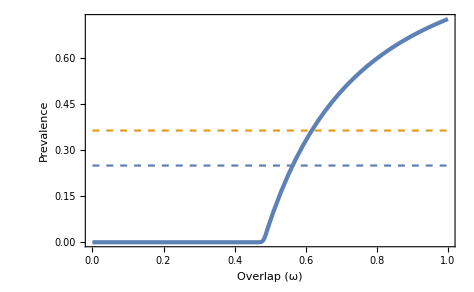

```mathematica
Show[With[{κ=0.458,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
(*ω=1 0.45,*)
β=0.0021},
Plot[{Iw[5000]/(Sw[5000]+Iw[5000])}/.NDSolve[
{L'[t]==δ λ (ω Iw[t])/(δ+μe)-μl L[t]-β L[t]ω(Sw[t]+Iw[t]),
Sw'[t]==-ω κ β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω  κ β Sw[t]L[t]-ρ Iw[t],
Sw[0]==29, Iw[0]==1, L[0]==0},
{Iw,L,Sw},
{t,0,5000}],
{ω,0,1},
Frame->True,FrameTicks->{{True,False},{True,False}},
PlotTheme->{ "LargeLabels","ThickLines","SizeScale"},
FrameLabel->{"Overlap (ω)","Prevalence"}]],
Plot[{0.25,0.364},{x,0,1}, PlotStyle->Dashed]]
```

We can do the same, with a dog-only model.

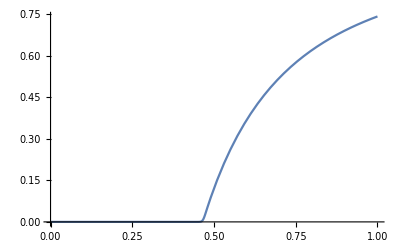

```mathematica
With[{κ=0.485,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
(*ω=1 0.45,*)
β=0.0021},
Plot[{Iw[5000]/(Sw[5000]+Iw[5000])}/.
NDSolve[
{L'[t]==δ λ (ω Iw[t])/(δ+μe)-μl L[t]-β L[t]ω(Sw[t]+Iw[t]),
Sw'[t]==-ω κ β Sw[t]L[t]+ρ Iw[t],
Iw'[t]==ω  κ β Sw[t]L[t]-ρ Iw[t],
Sw[0]==29, Iw[0]==1, L[0]==0},
{Iw,L,Sw},
{t,0,5000}],
{ω,0,1}]]
```

```mathematica
With[{κ=0.485,σ=1 0.030,
λ=1/0.6,
μl=1/6.6,δ=0.044,μe=0.069,
ρ=1/42,
ω=1. 0.358,
β=0.0021},
Evaluate[Simplify[{Iw/(Sw+Iw),Id/(Id+Sd)}/.catsol[[1]]]]]
```

{(0.0000109387 L)/(1/42+0.0000109387 L),(0.0010185 L)/(1/42+0.0010185 L)}

```mathematica
catsol=Solve[{-j β Sd L+ρ Id,
j β Sd L-ρ Id,
m bd Id/(m+z)-μ L-β L(Sd+Id)}=={0,0,0}, {Sd,Id,L}]
Simplify[Iw/(Sw+Iw)/.catsol]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Sd→-((m+z) μ ρ)/(β (-bd j m+j L m β+j L z β+m ρ+z ρ)),Id→-(j L (m+z) μ)/(-bd j m+j L m β+j L z β+m ρ+z ρ)},{Id→0,L→0}}

{Iw/(Iw+Sw),Iw/(Iw+Sw)}

SystemDialogInput::nprmtv: SystemDialogInput is not currently supported within preemptive evaluations.